## Loading FeynCalc and FeynArts

We allow CKM mixing.

```mathematica
If[ $FrontEnd === Null,
		$FeynCalcStartupMessages = False;
		Print["Computation of the total decay rate for a b quark going into a c quark, 
a tauon and a tauon antineutrino in Electroweak Theory at tree level."];
];
If[$Notebooks === False, $FeynCalcStartupMessages = False];
$LoadFeynArts= True;
<<FeynCalc`
$FAVerbose = 0;
$CKM = True;
```

FeynCalc is already loaded! To reload it, please restart the kernel.

$Aborted

## Generate Feynman diagrams

This is done using FeynArts. As with the example, the computation is carried out in the unitary gauge to avoid Goldstone bosons.

```mathematica
InitializeModel[{SM, UnitarySM}, GenericModel -> {Lorentz, UnitaryLorentz}];
```

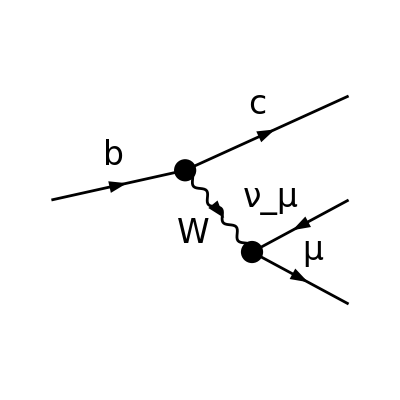

```mathematica
topBDecayTree = CreateTopologies[0, 1 -> 3];
diagsBDecayTree = InsertFields[topBDecayTree, {F[4, {3}]} -> {F[3,
		{2}],-F[1,{2}],F[2,{2}]}, InsertionLevel -> {Classes},
		Model -> {SM, UnitarySM},GenericModel->{Lorentz, UnitaryLorentz}];
Paint[diagsBDecayTree, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->False];
```

## Obtain the amplitude

```mathematica
ampBDecayTree=FCFAConvert[CreateFeynAmp[diagsBDecayTree,Truncated -> False],List->False,SMP->True,ChangeDimension->4,
IncomingMomenta->{p},OutgoingMomenta->{k,q1,q2},DropSumOver->True,
FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2] SMP["G_F"] SMP["m_W"]^-2SMP["sin_W"]^2]}]//Contract
```

(2 √2 CKM(2,3) G_F δ_Col1Col2 (φ(OverBar[q2],m_μ)).(γ̄)^Lor2.(γ̄)^7.(φ(-OverBar[q1])) (φ(k̄,m_c)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,m_b)))/(m_W^2 ((OverBar[q1]+OverBar[q2])^2-m_W^2))

## Set up the kinematics

```mathematica
FCClearScalarProducts[]
SP[k,k]=SMP["m_c"]^2;
SP[q1,q1]=0;
SP[q2,q2]=SMP["m_tau"]^2;
```

## Obtain squared amplitude for the unpolarized process

```mathematica
sqAmpBDecayTree = ampBDecayTree ComplexConjugate[FCRenameDummyIndices[ampBDecayTree]]//
FermionSpinSum[#,ExtraFactor -> 1/2]&//ReplaceAll[#, DiracTrace :> Tr]&//Contract//Factor2
```

(32 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 ((k̄·OverBar[q2]) (p̄·OverBar[q1]) (1/((OverBar[q1]+OverBar[q2])^2-m_W^2))^2-(k̄·OverBar[q1]) (p̄·OverBar[q2]) (1/((OverBar[q1]+OverBar[q2])^2-m_W^2))^2+(k̄·OverBar[q2]) (p̄·OverBar[q1]) (1/((OverBar[q1]+OverBar[q2])^2-m_W^2))^2+(k̄·OverBar[q1]) (p̄·OverBar[q2]) (1/((OverBar[q1]+OverBar[q2])^2-m_W^2))^2))/m_W^4

```mathematica
sqAmpBDecayTree2=(FCE[sqAmpBDecayTree]/.{k+q1->0})//PropagatorDenominatorExplicit
```

(64 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄·OverBar[q2]) (p̄·OverBar[q1]))/(m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)

## Total decay rate for the unpolarized process

```mathematica
prefac=(2SMP["m_b"] (2Pi)^5 8)^-1;
diffDecayRate = prefac d3q1/En[q1] d3q2/En[q2] d3k/En[k] delta4[q-q1-q2] sqAmpBDecayTree2
```

(d3k d3q1 d3q2 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄·OverBar[q2]) (p̄·OverBar[q1]) delta4(q-q1-q2))/(8 π^5 m_b En(k) En(q1) En(q2) m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)

```mathematica
q1q2[mu_,nu_]:=ReplaceAll[Tdec[{{q1x,mu},{q2x,nu}},{q},List->False,Dimension->4],
{SP[q1x,q2x]->SP[q,q]/2, SP[q,q1x|q2x]->SP[q,q]/2}];
```

```mathematica
q1q2[mu,nu]//Factor2
```

1/12 ((q̄)^2 (ḡ)^munu+2 (q̄)^mu (q̄)^nu)

```mathematica
diffDecayRate1=Uncontract[diffDecayRate,q1,q2,Pair->All]
```

(d3k d3q1 d3q2 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄)^($AL$16391(1)) (p̄)^($AL$16392(1)) OverBar[q1]^($AL$16392(1)) OverBar[q2]^($AL$16391(1)) delta4(q-q1-q2))/(8 π^5 m_b En(k) En(q1) En(q2) m_W^4 (2 OverBar[q1]^($AL$16391(2)) OverBar[q2]^($AL$16391(2))+m_τ^2-m_W^2)^2)

```mathematica
diffDecayRate2=((diffDecayRate1//FCE)/. FV[q1,mu_]FV[q2,nu_]:>q1q2[mu,nu])//Contract//FCE
```

(d3k d3q1 d3q2 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄·q̄) (p̄·q̄) delta4(q-q1-q2))/(48 π^5 m_b En(k) En(q1) En(q2) m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)+(d3k d3q1 d3q2 (q̄)^2 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄·p̄) delta4(q-q1-q2))/(96 π^5 m_b En(k) En(q1) En(q2) m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)

```mathematica
diffDecayRate3=diffDecayRate2/.{d3q2 delta4[q-q1-q2]-> delta[En[q]-2En[q1]]}/.{En[q2]->En[q1]}/.
{d3q1-> 4Pi dq10 En[q1]^2}/.{dq10 delta[En[q]-2En[q1]]->1/2}
```

(d3k (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄·q̄) (p̄·q̄))/(24 π^4 m_b En(k) m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)+(d3k (q̄)^2 (CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (k̄·p̄))/(48 π^4 m_b En(k) m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)

```mathematica
diffDecayRate4=(diffDecayRate3//.{SP[q,p]->SMP["m_b"]^2-SMP["m_b"] En[k],SP[k,q]|SP[p,k]-> SMP["m_b"] En[k],
SP[q,q]-> SMP["m_b"]^2-2 SMP["m_b"]En[k]})//Simplify
```

-(d3k (CKM(2,3))^2 m_b G_F^2 δ_Col1Col2^2 (4 En(k)-3 m_b))/(48 π^4 m_W^4 (2 (OverBar[q1]·OverBar[q2])+m_τ^2-m_W^2)^2)

```mathematica
diffDecayRate5 = (diffDecayRate4 //. {2SP[q1,q2] -> SMP["m_b"]^2 + SMP["m_c"]^2 - SMP["m_tau"]^2 -2SMP["m_b"]En[k]}) // Simplify
```

-(d3k (CKM(2,3))^2 m_b G_F^2 δ_Col1Col2^2 (4 En(k)-3 m_b))/(48 π^4 m_W^4 (-2 m_b En(k)+m_b^2+m_c^2-m_W^2)^2)

```mathematica
diffDecayRate6=(diffDecayRate5/.d3k-> dk0 En[k]^2 4Pi /. En[k]-> Eps SMP["m_b"]/2/. 
dk0-> dEps SMP["m_b"]/2)// Factor2
```

(dEps (3-2 Eps) Eps^2 (CKM(2,3))^2 m_b^5 G_F^2 δ_Col1Col2^2)/(96 π^3 m_W^4 (-Eps m_b^2+m_b^2+m_c^2-m_W^2)^2)

```mathematica
decayRateTotal=Integrate[diffDecayRate6/.dEps->1,{Eps,0,1}]
```

ConditionalExpression[-((CKM(2,3))^2 G_F^2 δ_Col1Col2^2 (m_b^6/(m_W^2-m_c^2)+6 m_b^2 (m_c^2-m_W^2) (-log(-m_b^2-m_c^2+m_W^2)+log(m_W^2-m_c^2)+1)+6 (m_c^2-m_W^2)^2 (log(m_W^2-m_c^2)-log(-m_b^2-m_c^2+m_W^2))+3 m_b^4))/(96 π^3 m_b^3 m_W^4),(m_c^2-m_W^2)/m_b^2+1<0∨(Re((m_W^2-m_c^2)/m_b^2)<0∧(Re((m_c^2-m_W^2)/m_b^2)≤-1∨Re((m_c^2-m_W^2)/m_b^2)≥0))∨(m_c^2-m_W^2)/m_b^2∉ℝ]